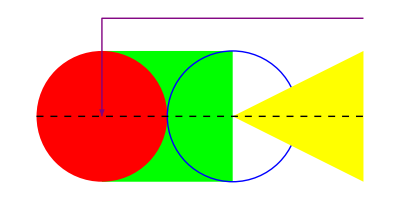

```mathematica
Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}]
```

Initial Conditions:

```mathematica
basis={{1,0},{0.5,Sqrt[3]/2}}; (* A basis generating the lattice points. Length equal to dimension of lattice.*)
rowLength[n_Integer]:=If[EvenQ[n],{n/2,n/2},{(n+1)/2,(n-1)/2}]; (*First value is odd trangles*)
r=rowLength[7]; (* Specifies how many "odd" and "even" triangles are in our graphic. *)
c={0,1,0,0.5,1,1,0}; (* Initial conditions. *)
```

Triangular Array Case:

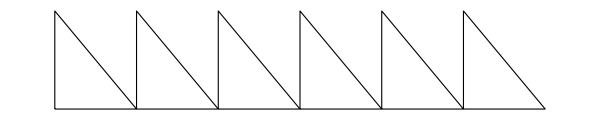

```mathematica
oddTriangles[basis_,rowLength_,initialConditions_]:=
Table[
{FaceForm[GrayLevel[1-initialConditions[[2*i+1]]]],EdgeForm[Black],Triangle[{i*basis[[1]]+{0,0},i*basis[[1]]+basis[[1]],i*basis[[1]]+basis[[2]]}]},
{i,0,rowLength[[1]]-1}]; (* Generates the "odd" traingles that can then be interpreted as Graphics objects. *)
Graphics[oddTriangles[basis,r,c],ImageSize->100*r[[1]]]
```

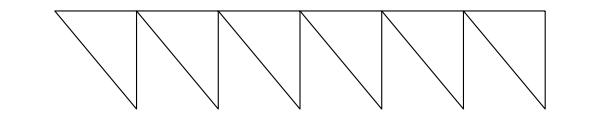

```mathematica
evenTriangles[basis_,rowLength_,initialConditions_]:=
Table[
{FaceForm[GrayLevel[1-initialConditions[[2*(i+1)]]]],EdgeForm[Black],
Triangle[{(i+1)*basis[[1]]+basis[[2]],i*basis[[1]]+basis[[1]],i*basis[[1]]+basis[[2]]}]},
{i,0,rowLength[[2]]-1}];(* Generates the "even" traingles that can then be interpreted as Graphics objects. *)
Graphics[evenTriangles[basis,r,c],ImageSize->100*r[[2]]]
```

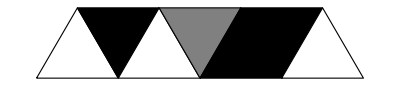

```mathematica
triangleCA[basis_,rowLength_,initialConditions_]:=
Graphics[Riffle[
oddTriangles[basis,rowLength,initialConditions],evenTriangles[basis,rowLength,initialConditions]
],ImageSize->100*r[[1]]]; (* Combines the "odd" and "even" triangle lists and makes a graphic for them. *)
triangleCA[basis,r,c]
```